```mathematica
AGENT_ZERO MATHEMATICA NOTEBOOK
		                                                              Joshua M. Epstein
			                                                        August 15, 2013
```

## II.1. Complete Solution of the Rescorla-Wagner Model in Step Functions The following Mathematica 8.0 code implements equation [12], the complete acquisition and extinction trajectory for the Rescorla-Wagner Model, using Unit Step Functions. The subsequent Animate code generates Movie 0 of this entire trajectory as the parameter, n, is varied from 0 to 30 in increments of 0.1. A snapshot from the Movie is shown. The full Movie is posted as Animation 0 on the book’s Princeton website.

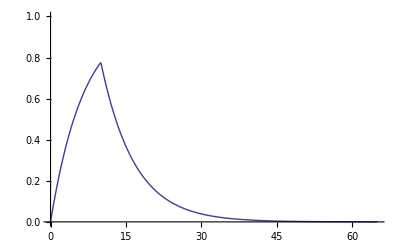

```mathematica
Plot[UnitStep[10-t](1-Exp[-.15t])+ UnitStep[t-10](1-Exp[-1.5])Exp[-.15(t-10)],{t,0,65},PlotRange->{0,1}]
```

```mathematica
Animate[Plot[UnitStep[n-t](1-Exp[-.15t])+ UnitStep[t-n](1-Exp[-.15n])Exp[-.15(t-n)],{t,0,65},PlotRange->{0,1}], {n,0,30,.1}]
```

II .2.  Two-Agent Dispositional Contagion. From Negative Disposition to Inititation of Action. 
The Four Panels of Figure 18 (includes Figure 16).

This entire section (and the next) can be compressed into a single Mathematica Module.  But for non-programmers, a step-by-step exposition
will be clearer.  We begin by defining three global constants (probabilities and a common threshold) that will be used throughout. Note that
Agent 1’s probability is zero.  Then we use Mathematica’s nonlinear ordinary differential equation solver, NDSolve, to generate a  
numerical solution to the Rescorla-Wagner equations, with initial affect equal to zero for both agents. The S-curve exponent, delta, is also
zero.  Mathematica reports when it has computed Interpolating Functions, a message we shall suppress.  Then we vary the weight of
Agent_2 on Agent_1 from zero to 0.9, showing the plots in each case. The pair of plots given in Figure 16 are the 0.7 case below.

```mathematica
p1=.00
p2=.80
Tau=1.0
```

0.

0.8

1.

```mathematica
rw15=NDSolve[{
		      v1'[t]==0.06(v1[t]^0)(1-v1[t]),
		      v2'[t]==0.02(v2[t]^0)(1-v2[t]),
                        v1[0]==.00,v2[0]==0.00},
                          {v1,v2},{t,650}]
```

{{v1→InterpolatingFunction[{{0.,650.}},<>],v2→InterpolatingFunction[{{0.,650.}},<>]}}

## 0 : Never positive

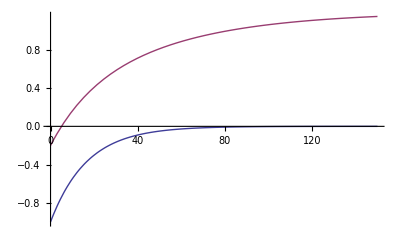

```mathematica
Plot[Evaluate[{v1[t]+p1+.0(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw15],{t,0,150}]
```

## .3 : Positive but always lower

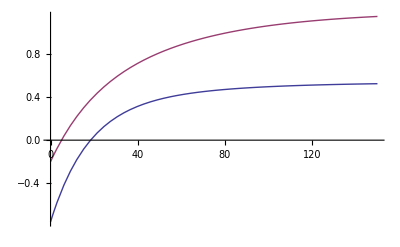

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw15],{t,0,150}]
```

## .7 : Supasses but goes second

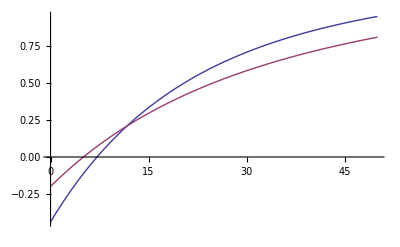

```mathematica
Plot[Evaluate[{v1[t]+p1+.7(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw15],{t,0,50}]
```

To plot the "phase portrait" of v1 on v2 with t a parameter, we use ParametricPlot.

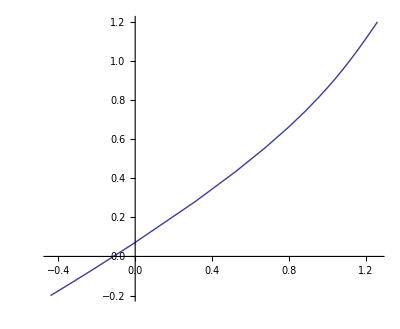

```mathematica
ParametricPlot[Evaluate[{v1[t]+p1+.7(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw15],{t,0,350}, PlotRange->All]
```

## .9 : Goes first

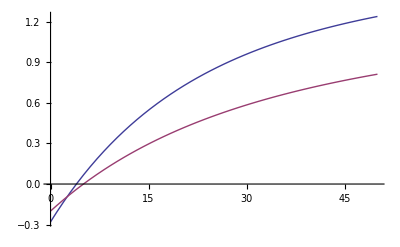

```mathematica
Plot[Evaluate[{v1[t]+p1+.9(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw15],{t,0,50}]
```

To properly compute dispositional extinction trajectories from t = 50, one must first pull out the 
  purely affective levels at that time and initialize the Rescorla - Wagner affective extinction variant 
  at those values, which happen to be 0.86 and 0.60. Then NDSolve is used with λ = 0 to generate 
  the purely affective extinction curves.  Finally, we add the probabilities and subtract the thresholds
  to yield the full dispositional extinction trajectories given in Figure 19.

```mathematica
rw16=NDSolve[{
		      v1'[t]==0.06(v1[t]^0)(0-v1[t]),
		      v2'[t]==0.02(v2[t]^0)(0-v2[t]),
                        v1[0]==.86,v2[0]==.60},
                          {v1,v2},{t,650}]
```

{{v1→InterpolatingFunction[{{0.,650.}},<>],v2→InterpolatingFunction[{{0.,650.}},<>]}}

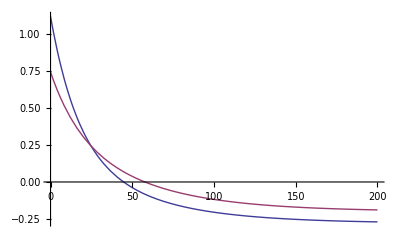

```mathematica
Plot[Evaluate[{v1[t]+p1+.9(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw16],{t,0,200}, PlotRange->All]
```

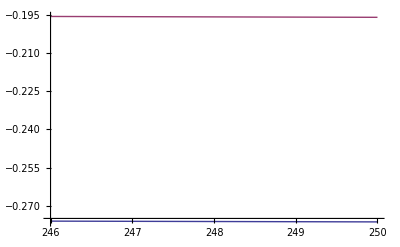

```mathematica
Plot[Evaluate[{v1[t]+p1+.9(v2[t]+p2)-Tau,
		      v2[t]+p2+.4(v1[t]+p1)- Tau
	                 }/.rw16],{t,246,250}]
```

## II. 3. Three - Agent Runs : Homogeneous Classical Rescorla - Wagner Learners and Heterogeneous Non - Classical (Generalized) Rescorla - Wagner Learners.

First, we generate the pair of runs in Figure 25. Agent 3 is the protagonist.  In the first run, he assigns zero weight to the    two agents, who are identical 
(so their curves coincide). With no learning, Agent 3 sits at minus Tau.   With maximal learning (weights of 1.0), he goes first.  As discussed in the text,
 three agents is the minimum number required for this phenomenon. Agents 1, 2, and 3 are red, blue, and green, respectively.

```mathematica
p1=.60
p2=.60
p3=.0
Tau=1.5
```

0.6

0.6

0.

1.5

```mathematica
rw2=NDSolve[{
		      v1'[t]==.1(v1[t]^.0)(1-v1[t]),
		      v2'[t]==.1(v2[t]^.0)(1-v2[t]),
                         v3'[t]==.0(v3[t]^.0)(1-v3[t]),
                        v1[0]==v2[0]==v3[0]==.0001},
                         {v1,v2,v3},{t,300}]
```

{{v1→InterpolatingFunction[{{0.,300.}},<>],v2→InterpolatingFunction[{{0.,300.}},<>],v3→InterpolatingFunction[{{0.,300.}},<>]}}

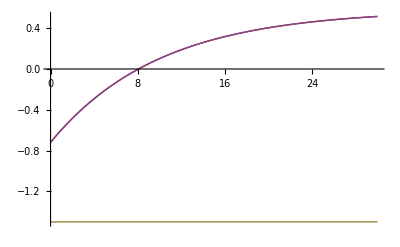

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2)+ .0(v3[t]+p3)-Tau,
		      v2[t]+p2+.3(v1[t]+p1)+.0(v3[t]+p3)- Tau,
	               v3[t]+p3+0(v2[t]+p2)+0(v1[t]+p3)-Tau}/.rw2],{t,0,30}, PlotRange->All]
```

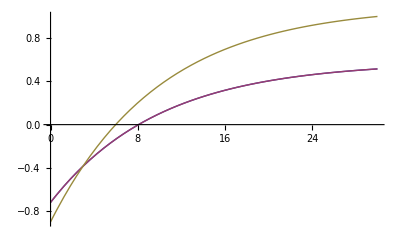

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2)+ .0(v3[t]+p3)-Tau,
		      v2[t]+p2+.3(v1[t]+p1)+.0(v3[t]+p3)- Tau,
	               v3[t]+p3+1(v2[t]+p2)+1(v1[t]+p3)-Tau}/.rw2],{t,0,30}, PlotRange->All]
```

Next we exploit the heterogeneity afforded by the generalized model, generating the plots of Figure 22. Agent 3 remains 
a classical learner. But the others have diverse probability estimates, and δ exponents which make them S - curve learners. 
As usual, we first apply NDSolve to the generalized system of differenial equations, and then show two plots.  With zero 
weights, Agent 3 never acts. With a weight of .475, he acts first, and ends with the highest disposition.  Notice that, as per fn.107, 
 since δ>0, v(0)=0 would suppress all dynamics, so we use 0.0001 here and, purely for comparability, in rw2 above.

```mathematica
p1=.80
p2=.60
p3=.00
Tau=1.5
```

0.8

0.6

0.

1.5

```mathematica
rw6=NDSolve[{
		      v1'[t]==.10 (v1[t]^1)(1-v1[t]),
		      v2'[t]==.03(v2[t]^.5)(1-v2[t]),
                         v3'[t]==.02(v3[t]^.0)(1-v3[t]),
                        v1[0]==v2[0]==v3[0]==.0001},
                         {v1,v2,v3},{t,300}]
```

{{v1→InterpolatingFunction[{{0.,300.}},<>],v2→InterpolatingFunction[{{0.,300.}},<>],v3→InterpolatingFunction[{{0.,300.}},<>]}}

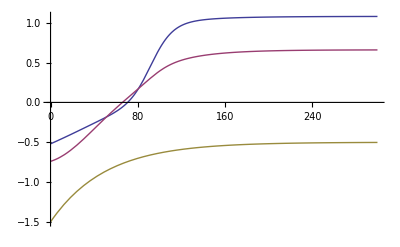

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+p3+0(v1[t]+p1+v2[t]+p2)-Tau}/.rw6],{t,0,300}, PlotRange->All]
```

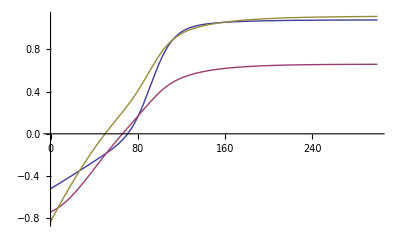

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+p3+.475(v1[t]+p1+v2[t]+p2)-Tau}/.rw6],{t,0,300}, PlotRange->All]
```

```mathematica
Extinction Phase
```

Now, we generate the two extinction curves of Figures 22 and 23.  In the first, no one has 
post - traumatic stress, and can reset their λ - values to zero.  In the second, Agent 3 can only 
reset to 0.95, radically delaying her recovery (until t = 750), and substantially delaying 
everyone else' s. As before,we first solve the generalized Rescorla - Wagner equations for the 
purely affective trajectories, initializing at whatever value they attained when extinction begins.  In 
this case, it is clear from the horiziontal net dispositions that the v-trajectories are close to their 
asymptotic values of 1.0,which we shall use.  However, were that not the case, a cute way to extract 
approximate values,circumventing inspection of the interploating functions, is to simply plot the 
affects from 299 to 300, for example, with the command : 

Plot[Evaluate[{v3[t], v2[t], v1[t]} /. rw6], {t, 299, 300}]

The extinction computations follow:

```mathematica
rw7=NDSolve[{
		      v1'[t]==.10 (v1[t]^1)(-v1[t]),
		      v2'[t]==.03(v2[t]^.5)(-v2[t]),
                         v3'[t]==.02(v3[t]^.0)(-v3[t]),
                        v1[0]==1, v2[0]==1, v3[0]==1.0},
                         {v1,v2,v3},{t,3000}]
```

{{v1→InterpolatingFunction[{{0.,3000.}},<>],v2→InterpolatingFunction[{{0.,3000.}},<>],v3→InterpolatingFunction[{{0.,3000.}},<>]}}

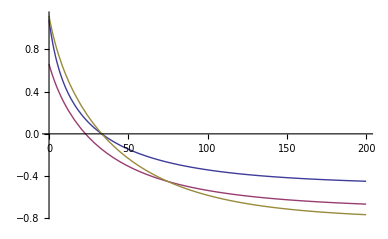

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+0+.475(v2[t]+p2+v1[t]+p1)-Tau}/.rw7],{t,0,200}, PlotRange->All]
```

```mathematica
Asymptotic values are suggested by running to t=3000, as follows.
```

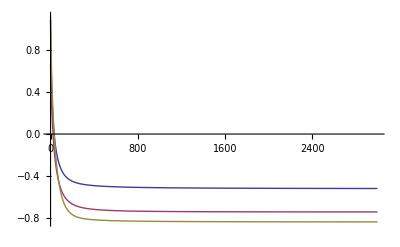

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+0+.475(v2[t]+p2+v1[t]+p1)-Tau}/.rw7],{t,0,3000}, PlotRange->All]
```

```mathematica
rw8=NDSolve[{
		      v1'[t]==.10 (v1[t]^1)(-v1[t]),
		      v2'[t]==.03(v2[t]^.5)(-v2[t]),
                         v3'[t]==.02(v3[t]^.0)(.95-v3[t]),
                        v1[0]==1, v2[0]==1, v3[0]==1},
                         {v1,v2,v3},{t,3000}]
```

{{v1→InterpolatingFunction[{{0.,3000.}},<>],v2→InterpolatingFunction[{{0.,3000.}},<>],v3→InterpolatingFunction[{{0.,3000.}},<>]}}

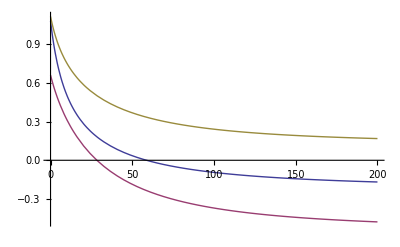

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+p3+.475(v2[t]+p2+v1[t]+p1)-Tau}/.rw8],{t,0,200}]
```

```mathematica
`
```

```mathematica
Asymptotic values are suggested by running to t=3000, as follows.
```

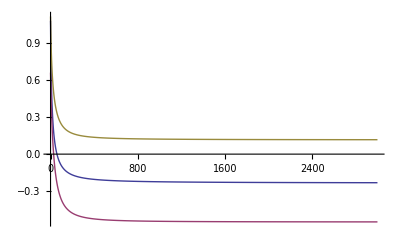

```mathematica
Plot[Evaluate[{v1[t]+p1+.3(v2[t]+p2+v3[t]+p3)-Tau,
		      v2[t]+p2+.2(v1[t]+p1+v3[t]+p3)- Tau,
	               v3[t]+p3+.475(v2[t]+p2+v1[t]+p1)-Tau}/.rw8],{t,0,3000}]
```

```mathematica
II.4  Group's Dispositional Trajectory in a Vector Field
```

```mathematica
j1=VectorPlot3D[{-x,-y,-z}, {x,0,3},{y,0,3}, {z,0,3}]
```

-Graphics3D-

```mathematica
j2=ParametricPlot3D[{t,2t,4Sin[t]},{t,0,3},PlotStyle->{Thick,Red}]
```

-Graphics3D-

```mathematica
Show[j1,j2]
```

-Graphics3D-

## II .5. Strength - Homophily Weight Surface Here we plot the weight as a function of affective stength and homophily.

```mathematica
Plot3D[(x+y) (1-Abs[x-y]), {x,0,1},{y,0,1}]
```

-Graphics3D-

Here, we give Mathematica Code for Figures 51, 51, and 52, where all agents are non - classical with heterogeneous positive
δ values. First, we plot net dispositions. Next we plot only the inter - agent weights over time. In both cases, the weight is the sum of 
affective values, times one minus the absolute value of the affective difference. Third, the dynamic weight vector traces acurve in 3-Space.

```mathematica
p1=.80
p2=.80
p3=.80
Tau=1.5
```

0.8

0.8

0.8

1.5

```mathematica
rw9=NDSolve[{
		      v1'[t]==.1 (v1[t]^1.0)(1-v1[t]),
		      v2'[t]==.1(v2[t]^0.8)(1-v2[t]),
                         v3'[t]==.1(v3[t]^0.2)(1-v3[t]),
                        v1[0]==v2[0]==v3[0]==.0001},
                         {v1,v2,v3},{t,600}]
```

{{v1→InterpolatingFunction[{{0.,600.}},<>],v2→InterpolatingFunction[{{0.,600.}},<>],v3→InterpolatingFunction[{{0.,600.}},<>]}}

```mathematica
Dispositional Trajectories with new weights
```

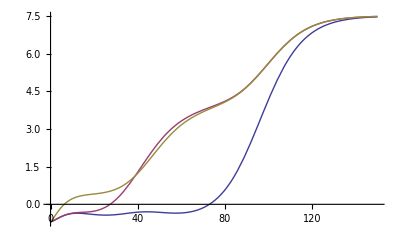

```mathematica
d9=Plot[Evaluate[{v1[t]+p1+ (v1[t]+v2[t])(1-Abs[v1[t]-v2[t]]) (v2[t]+p2)+ (v1[t]+v3[t])(1-Abs[v1[t]-v3[t]] ) (v3[t]+p3)-Tau,
                         v2[t]+p2+ (v1[t]+v2[t])(1-Abs [v2[t]-v1[t]]) (v1[t]+p1) +(v2[t]+v3[t]) (1-Abs[v2[t]-v3[t]])(v3[t]+p3)- Tau,
	               v3[t]+p3+ (v2[t]+v3[t])(1-Abs[v3[t]-v2[t]])(v2[t]+p2)+ (v1[t]+v3[t])(1-Abs[v3[t]-v1[t]]) (v1[t]+p3)-Tau}/.rw9],{t,0,150}]
```

```mathematica
Affects alone converge to 1.0
```

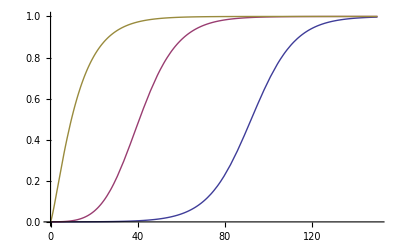

```mathematica
a9=Plot[Evaluate[{v1[t], v2[t],v3[t]}/.rw9],{t,0,150}]
```

```mathematica
Weights alone.  Start at zero, converge to 2, since this is sum of affects each bounded above by 1
```

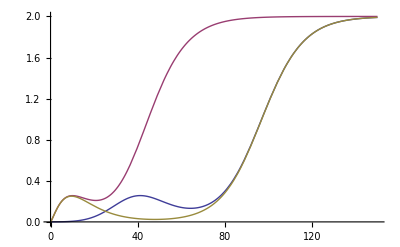

```mathematica
w9=Plot[Evaluate[{(v1[t]+v2[t]) (1-Abs[v1[t]-v2[t]]),(v2[t]+v3[t]) (1-Abs[v2[t]-v3[t]]),(v1[t]+v3[t])(1-Abs[v3[t]-v1[t]])}/.rw9],{t,0,150}]
```

```mathematica
Group affinity curve in 3 - Space.
```

```mathematica
ParametricPlot3D[Evaluate[{(v1[t]+v2[t]) (1-Abs[v1[t]-v2[t]]),(v2[t]+v3[t]) (1-Abs[v2[t]-v3[t]]),(v1[t]+v3[t])(1-Abs[v3[t]-v1[t]])}/.rw9],{t,0,150},PlotStyle->{Thick,Red}, AxesLabel->{"ω12","ω23","ω31"}]
```

-Graphics3D-

```mathematica
rw10=NDSolve[{
		      v1'[t]==.01(v1[t]^1.0)(1-v1[t]),
		      v2'[t]==.04(v2[t]^0.8)(1-v2[t]),
                         v3'[t]==.08(v3[t]^0.2)(1-v3[t]),
                        v1[0]==v2[0]==v3[0]==.0001},
                         {v1,v2,v3},{t,1800}]
```

{{v1→InterpolatingFunction[{{0.,1800.}},<>],v2→InterpolatingFunction[{{0.,1800.}},<>],v3→InterpolatingFunction[{{0.,1800.}},<>]}}

```mathematica
ParametricPlot3D[Evaluate[{(v1[t]+v2[t]) (1-Abs[v1[t]-v2[t]]),(v2[t]+v3[t]) (1-Abs[v2[t]-v3[t]]),(v1[t]+v3[t])(1-Abs[v3[t]-v1[t]])}/.rw10],{t,0,200},PlotStyle->{Thick,Red}, AxesLabel->{"ω12","ω23","ω31"}, PlotRange->All]
```

-Graphics3D-